# AntonAntonov/UMLDiagramGeneration

UML diagrams generation by introspection and direct specs

## Paclet Manifest

"Documentation"

"English"

"Guides"

"UMLdiagramsgeneration.nb"DocumentationEnglishGuidesUMLdiagramsgeneration.nb

"ReferencePages"

"Symbols"

"JavaPlantUML.nb"DocumentationEnglishReferencePagesSymbolsJavaPlantUML.nb

"PlantUMLSpec.nb"DocumentationEnglishReferencePagesSymbolsPlantUMLSpec.nb

"PythonWebPlantUML.nb"DocumentationEnglishReferencePagesSymbolsPythonWebPlantUML.nb

"SubValueReferenceRules.nb"DocumentationEnglishReferencePagesSymbolsSubValueReferenceRules.nb

"UMLClassGraph.nb"DocumentationEnglishReferencePagesSymbolsUMLClassGraph.nb

"UMLClassNode.nb"DocumentationEnglishReferencePagesSymbolsUMLClassNode.nb

"Tutorials"

"Kernel"

"UMLDiagramGeneration.wl"KernelUMLDiagramGeneration.wl

"LICENSE"LICENSE

"PacletInfo.wl"PacletInfo.wl

"README.md"README.md

"ResourceDefinition.nb"ResourceDefinition.nb

## Web Content

### Headline Image

### Basic Description

This package has functions for the generation Unified Modeling Language (UML) diagrams according to specified relationships of symbols that represent classes and by introspection of code.

### Details

The main function, UMLClassGraph, can handle both (i) direct class specifications, and (ii) class names from Object-Oriented Programming (OOP) implementations.

The function UMLClassGraph takes all options of Graph.

The functions PlantUMLSpec converts UML spec into a PlantUML spec.

There are two different functions for getting PlantUML imags using Java or Python.

### Primary Context

AntonAntonov`UMLDiagramGeneration`

### Main Guide Page

## Examples

### Initialization for Examples

```mathematica
PacletDirectoryLoad[NotebookDirectory[]];
```

```mathematica
Needs["AntonAntonov`UMLDiagramGeneration`"];
```

### Basic Examples

Let us visualize a simple relationship between buildings, people, books, and a client program:

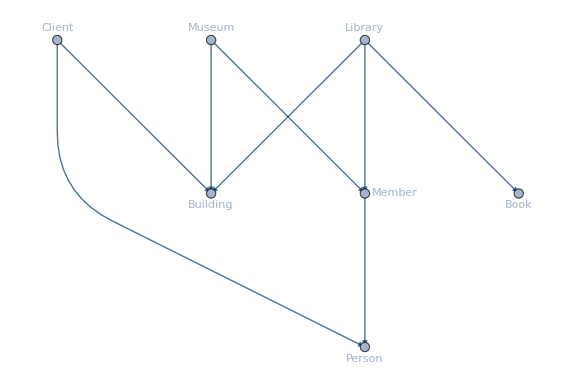

```mathematica
UMLClassGraph[
{Library->Building,Museum->Building,Member->Person},
{},
{Library->Member,Museum->Member,Client->Building,Client->Person},{Library->Book},
"Abstract"->{Building,Person},"EntityColumn"->False,VertexLabelStyle->"Text",ImageSize->Large,GraphLayout->"LayeredDigraphEmbedding"]
```

In the diagram above the classes Person and Building are abstract (that is why are in italic). Member inherits Person, Library and Museum inherit Building. Library can contain (many) Book objects and it is associated with Member. Client associates with Building and Person.

### Scope

Let us look into a simple UML generation example for the design pattern Template Method. Here is the Wolfram Language (WL) code for that design pattern:

```mathematica
Clear[AbstractClass,ConcreteOne,ConcreteTwo];

CLASSHEAD=AbstractClass;
AbstractClass[d_]["Data"[]]:=d;
AbstractClass[d_]["PrimitiveOperation1"[]]:=d[[1]];
AbstractClass[d_]["PrimitiveOperation2"[]]:=d[[2]];
AbstractClass[d_]["TemplateMethod"[]]:=CLASSHEAD[d]["PrimitiveOperation1"[]]+CLASSHEAD[d]["PrimitiveOperation2"[]]

ConcreteOne[d_][s_]:=Block[{CLASSHEAD=ConcreteOne},AbstractClass[d][s]]
ConcreteOne[d_]["PrimitiveOperation1"[]]:=d[[1]];
ConcreteOne[d_]["PrimitiveOperation2"[]]:=d[[1]]*d[[2]];

ConcreteTwo[d_][s_]:=Block[{CLASSHEAD=ConcreteTwo},AbstractClass[d][s]]
ConcreteTwo[d_]["PrimitiveOperation1"[]]:=d[[1]];
ConcreteTwo[d_]["PrimitiveOperation2"[]]:=d[[3]]^d[[2]];
```

Here is the corresponding UML diagram:

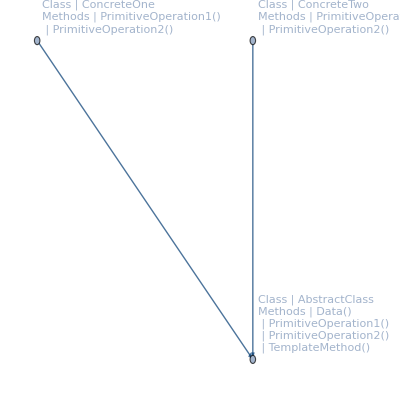

```mathematica
UMLClassGraph[{AbstractClass,ConcreteOne,ConcreteTwo}]
```

Here is a restyled version of the diagram above:

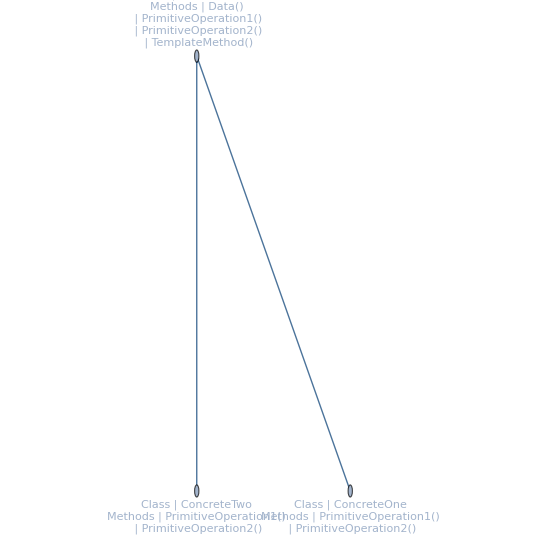

```mathematica
UMLClassGraph[{AbstractClass,ConcreteOne,ConcreteTwo},{"AbstractMethods"->{"PrimitiveOperation1","PrimitiveOperation2"}},"Abstract"->{AbstractClass},VertexLabelStyle->"Subsubsection",GraphLayout->{"LayeredDigraphEmbedding", "Orientation"->Bottom}]
```

Here is an example of UMLClassNode usage:

```mathematica
Grid@Table[UMLClassNode[AbstractClass,"Abstract"->a,"EntityColumn"->ec],{a,{{},{"PrimitiveOperation1","PrimitiveOperation2",AbstractClass}}},{ec,{False,True}}]
```

AbstractClass
Data[]
PrimitiveOperation1[]
PrimitiveOperation2[]
TemplateMethod[] | Class | AbstractClass
Methods | Data[]
 | PrimitiveOperation1[]
 | PrimitiveOperation2[]
 | TemplateMethod[]
AbstractClass
PrimitiveOperation1
PrimitiveOperation2
AbstractClass
Data[]
PrimitiveOperation1[]
PrimitiveOperation2[]
TemplateMethod[] | Class | AbstractClass
Methods | PrimitiveOperation1
 | PrimitiveOperation2
 | AbstractClass
 | Data[]
 | PrimitiveOperation1[]
 | PrimitiveOperation2[]
 | TemplateMethod[]

Here is an example of PlantUML usage:

```mathematica
PlantUMLSpec["Parents"->{"MyPackageClass::D"->"MyPackageClass::C","MyPackageClass::D"->"MyPackageClass::A","MyPackageClass::D"->"MyPackageClass::B","MyPackageClass::C"->"MyPackageClass::A"},"AbstractMethods"->{"MyPackageClass::A"->{"a1"},"MyPackageClass::B"->{"b1"}},"RegularMethods"->{"MyPackageClass::D"->{"BUILDALL","b1","d1"},"MyPackageClass::C"->{"BUILDALL","a1","c1"}},"Abstract"->{"MyPackageClass::A","MyPackageClass::B","MyPackageClass::A"}]
```

@startuml
abstract MyPackageClass::A{
 {abstract} a1
}

abstract MyPackageClass::B{
 {abstract} b1
}

class MyPackageClass::C{
 BUILDALL
 a1
 c1
}
MyPackageClass::C --> MyPackageClass::A

class MyPackageClass::D{
 BUILDALL
 b1
 d1
}
MyPackageClass::D --> MyPackageClass::C
MyPackageClass::D --> MyPackageClass::A
MyPackageClass::D --> MyPackageClass::B
@enduml

Here is the image generated by PlantUML:

-Graphics-

## Source & Additional Information

### Creator

Anton Antonov

### Source Control Repository

https://github.com/antononcube/WL-UMLDiagramGeneration-paclet

### License

MIT License [»](https://resources.wolframcloud.com/PacletRepository/licenses/MIT)
 Apache License 2.0 [»](https://resources.wolframcloud.com/PacletRepository/licenses/Apache-2.0)
 Creative Commons Zero v1.0 Universal [»](https://resources.wolframcloud.com/PacletRepository/licenses/CC0-1.0)
 NoneA license is not required for personal deployments

### Keywords

Code generation

Introspection

PlantUML

UML

Unified Modeling Language

### Categories

Cloud & Deployment
 Data Manipulation & Analysis
 External Interfaces & Connections
 Geographic Data & Computation
 Graphs & Networks
 Images
 Machine Learning
 Scientific and Medical Data & Computation
 Sound & Video
 Symbolic & Numeric Computation
 Time-Related Computation
 Visualization & Graphics |  Core Language & Structure
 Engineering Data & Computation
 Financial Data & Computation
 Geometry
 Higher Mathematical Computation
 Knowledge Representation & Natural Language
 Notebook Documents & Presentation
 Social, Cultural & Linguistic Data
 Strings & Text
 System Operation & Setup
 User Interface Construction

### Related Resource Objects

AntonAntonov/CallGraph

AntonAntonov/MermaidJS

MermaidInk

### Original Source References and Attributions

Anton Antonov, "UML Diagrams Creation and Generation", (2016), Wolfram Community.

### Links

Anton Antonov, "Object Oriented Design Patterns", WTC-2015 presentation.

### Compatibility

#### Wolfram Language Version

10.3.1+

#### Operating System

Windows |  Mac |  Linux

#### Environments

SessionLocal or cloud interactive session
 WebEvaluationCloud evaluation initiated by an HTTP request
 BatchJobRemote batch job |  ScriptScript run in batch mode
 WebAPIAPI called through an HTTP request
 |  SubkernelParallel or grid subkernel
 ScheduledScheduled task

#### Cloud Support

Supported in cloud

#### Required Features

Notebooks |  Parallel Kernels |  Cloud Access

### Disclosures

Local filesDisclosuresLocalFilesChoose this option if your paclet directly does any of the following during loading or normal usage:
◼ Creates, deletes or modifies local files
◼ Imports data from local files
File operations related to normal paclet installation and loading are excepted.Click for more information

Wolfram accountDisclosuresWolframAccountChoose this option if your paclet directly does any of the following:
◼ Requires, uses, or records any information related to user’s Wolfram ID
◼ Interacts with the user’s Cloud account or Wolfram account
◼ Creates, deletes or modifies the user’s cloud objects
◼ Creates or executes cloud deployed scheduled tasks
◼ Uses cloud credits, service credits or Wolfram credits
◼ Makes WolframAlpha callsClick for more information

External servicesDisclosuresExternalServicesChoose this option if your paclet directly does any of the following:
◼ Makes requests to external services (http, ftp, ssh, etc)
◼ Creates or uses service connection
◼ Send emailsClick for more information

Wolfram Language system configurationDisclosuresWLSystemConfigurationChoose this option if your paclet directly does any of the following:
◼ Creates persistent local scheduled tasks
◼ Modifies WL system or environment settings
◼ Modifies $Path, Directory, or similar
◼ Installs additional paclets or dependencies
◼ Creates or imports non-public ResourceObject content
◼ Makes FrontEnd modifications
◼ Internal handlersClick for more information

Wolfram Language built-in symbolsDisclosuresWLSystemSymbolsChoose this option if your paclet directly modifies definitions of built-in symbols such as those in System` or other internal contexts.Click for more information

Paclet dependenciesDisclosuresPacletDependenciesChoose this option if your paclet directly installs or updates any additional paclets. Paclets that are included with the Wolfram system do not require a disclosure.Click for more information

OS configurationDisclosuresOSConfigurationChoose this option if your paclet directly does any of the following:
◼ Modifies OS settings
◼ Makes any use of SystemCredentialClick for more information

Local system interactionsDisclosuresLocalSystemInteractionsChoose this option if your paclet directly does any of the following:
◼ Executes Shell or RUN commands
◼ Uses external evaluators via ExternalEvaluate
◼ Interacts with external libraries
◼ Reads or writes to streams or sockets
◼ Launches parallel kernels, subkernels or GPUsClick for more information

OtherDisclosuresOtherAdd additional text as needed in a new cell below to document any additional disclosures that are not listed above.Click for more information

## Author Notes

Additional information about limitations, issues, etc.